```mathematica
SetDirectory[NotebookDirectory[]];
nodes = Import["nodes.txt"]//ToExpression;(* 10*10 nodes on a Cartesian grid of dimensions [-3,3]x[-3,3] *)
nodesM = Import["nodesM.txt"]//ToExpression;(* Only the mid 8*8 nodes, excluding those on boundary. *)
transNodes = Import["transNodes.txt"]//ToExpression;(* 4*4 nodes with the mid 2*2 randomly offset by a small amount. *)
transNodesM= Import["transNodesM.txt"]//ToExpression;(* The mid 8*8 randomly offset nodes. *)
```

```mathematica
lines1=Table[Line[{nodes[[i,1]],nodes[[i,10]]}],{i,1,10,3}];(* Horizontal lines corresponding to grid for 'nodes' *)
lines2=Table[Line[{nodes[[1,i]],nodes[[10,i]]}],{i,1,10,3}];(* Vertical lines corresponding to grid for 'nodes' *)
lines = Flatten[{lines1,lines2},1];(* All lines corresponding to grid for 'nodes' *)
linesM1=Table[Line[{nodes[[i,1]],nodes[[i,4]]}],{i,1,4}];(* Horizontal lines corresponding to grid for 'nodesM' *)
linesM2=Table[Line[{nodes[[1,i]],nodes[[4,i]]}],{i,1,4}];(* Vertical lines corresponding to grid for 'nodesM' *)
linesM=Flatten[{linesM1,linesM2},1];(* All lines corresponding to grid for 'nodesM' *)
transLines1 = Table[(* Horizontal lines corresponding to grid for 'transNodes' *)
	Line[Table[transNodes[[i,j]],{j,1,4}]],
	{i,1,4}
];
transLines2 = Table[(* Vertical lines corresponding to grid for 'transNodes' *)
	Line[Table[transNodes[[j,i]],{j,1,4}]],
	{i,1,4}
];
transLines=Flatten[{transLines1,transLines2},1];(* All lines corresponding to grid for 'transNodes' *)
transLinesM1=Table[(* Horizontal lines corresponding to grid for 'transNodesM' *)
	Line[Table[transNodesM[[i,j]],{j,1,2}]],
	{i,1,2}
];
transLinesM2= Table[(* Vertical lines corresponding to grid for 'transNodesM' *)
	Line[Table[transNodes[[j,i]],{j,1,2}]],
	{i,1,2}
];
transLinesM=Flatten[{transLinesM1,transLinesM2},1];(* All lines corresponding to grid for 'transNodesM' *)
```

```mathematica
lightSquares=Hold[{
	Polygon[{nodes[[1,1]],nodes[[1,4]],nodes[[4,4]],nodes[[4,1]]}],
	Polygon[{nodes[[7,1]],nodes[[7,4]],nodes[[10,4]],nodes[[10,1]]}],
	Polygon[{nodes[[4,4]],nodes[[4,7]],nodes[[7,7]],nodes[[7,4]]}],
	Polygon[{nodes[[1,7]],nodes[[1,10]],nodes[[4,10]],nodes[[4,7]]}],
	Polygon[{nodes[[7,7]],nodes[[7,10]],nodes[[10,10]],nodes[[10,7]]}]
};]
darkSquares={
	Polygon[{nodes[[4,1]],nodes[[4,4]],nodes[[7,4]],nodes[[7,1]]}],
	Polygon[{nodes[[4,7]],nodes[[4,10]],nodes[[7,10]],nodes[[7,7]]}],
	Polygon[{nodes[[1,4]],nodes[[1,7]],nodes[[4,7]],nodes[[4,4]]}],
	Polygon[{nodes[[7,4]],nodes[[7,7]],nodes[[10,7]],nodes[[10,4]]}]
};
```

Hold[{Polygon[{nodes⟦1,1⟧,nodes⟦1,4⟧,nodes⟦4,4⟧,nodes⟦4,1⟧}],Polygon[{nodes⟦7,1⟧,nodes⟦7,4⟧,nodes⟦10,4⟧,nodes⟦10,1⟧}],Polygon[{nodes⟦4,4⟧,nodes⟦4,7⟧,nodes⟦7,7⟧,nodes⟦7,4⟧}],Polygon[{nodes⟦1,7⟧,nodes⟦1,10⟧,nodes⟦4,10⟧,nodes⟦4,7⟧}],Polygon[{nodes⟦7,7⟧,nodes⟦7,10⟧,nodes⟦10,10⟧,nodes⟦10,7⟧}]};]

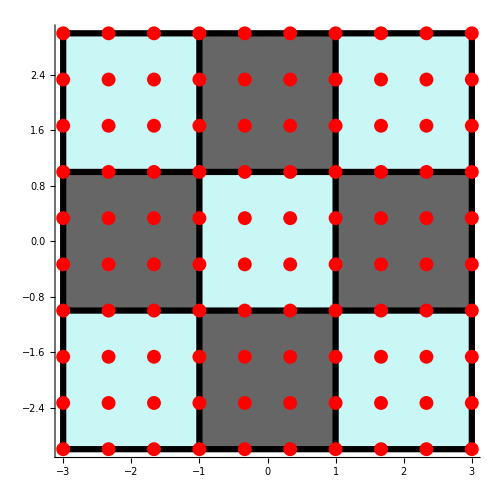

```mathematica
Graphics[
	{
		RGBColor["#a4f2f1"], Opacity[0.6],
		lightSquares,
		Black,
		darkSquares,
		Thickness[0.009],Opacity[1.0],
		lines,
		Red,PointSize[0.02],
		Point[Flatten[nodes,1]]
	},
	Axes->True,
	AxesOrigin->{-3.2,-3.2},
	AxesStyle->Directive[26, Black],
	ImageSize->500
]
```

```mathematica
lightSquares/.{"nodes"->"transNodes"}
```

Hold[{Polygon[{nodes⟦1,1⟧,nodes⟦1,4⟧,nodes⟦4,4⟧,nodes⟦4,1⟧}],Polygon[{nodes⟦7,1⟧,nodes⟦7,4⟧,nodes⟦10,4⟧,nodes⟦10,1⟧}],Polygon[{nodes⟦4,4⟧,nodes⟦4,7⟧,nodes⟦7,7⟧,nodes⟦7,4⟧}],Polygon[{nodes⟦1,7⟧,nodes⟦1,10⟧,nodes⟦4,10⟧,nodes⟦4,7⟧}],Polygon[{nodes⟦7,7⟧,nodes⟦7,10⟧,nodes⟦10,10⟧,nodes⟦10,7⟧}]};]

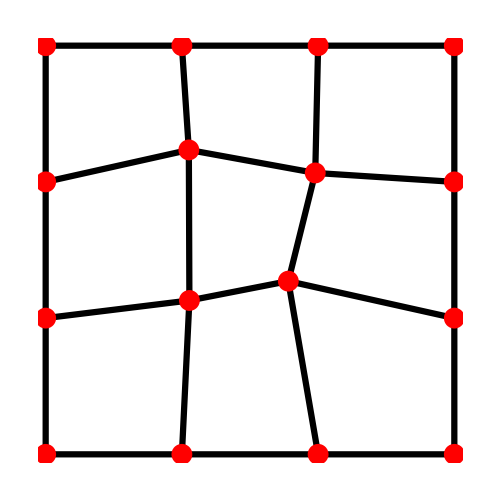

```mathematica
Graphics[
	{
		Black,Thickness[0.009],
		transLines,
		Red,PointSize[0.03],
		Point[Flatten[transNodes,1]]
	},
	ImageSize->500
]
```